```mathematica
MatrixPowExpand[A_,B_,k_]:=TensorExpand[Nest[#.(A+B)&,A+B,k-1]//Distribute,Assumptions->{A∈Matrices[{n,n}],B∈Matrices[{n,n}]}]
```

```mathematica
Δt=t/2;
U=TensorExpand[(IdentityMatrix[n]-I*(h1+h2)*t+1/2(-I*t)^2 MatrixPowExpand[h1,h2,2]+1/6(-I*t)^3 MatrixPowExpand[h1,h2,3]),Assumptions->{t∈Reals}];
trot1func[dt_]:=(IdentityMatrix[n]-I*h1*dt+1/2(-I*h1*dt).(-I*h1*dt));
trot2func[dt_]:=(IdentityMatrix[n]-I*h2*dt+1/2(-I*h2*dt).(-I*h2*dt));
trotFunc[A_,dt_]:=(IdentityMatrix[n]-I*A*dt+1/2(-I*dt)^2 MatrixPower[A,2]+1/6(-I*dt)^3 MatrixPower[A,3])
trotStep[dt1_,dt2_]:=trotFunc[h1,dt1].trotFunc[h2,dt2];
D[Collect[TensorExpand[U-trotStep[a1*Δt,b1*Δt].trotStep[(2-a1)*Δt,(2-b1)*Δt],Assumptions->{h1∈Matrices[{n,n}],h2∈Matrices[{n,n}],t∈Reals,a1∈Reals,b1∈Reals}],t,Simplify],{t,3}]/.{t->0,b1->-2/(-2+a1)}//FullSimplify
```

1/(4 (-2+a1))ⅈ ((-2+4 a1) h1.MatrixPower[h2,2]+(-2+a1) (-2+3 a1) h2.MatrixPower[h1,2]+4 MatrixPower[h1,2].h2-2 MatrixPower[h2,2].h1-8 h1.h2.h1+a1 ((-8+3 a1) MatrixPower[h1,2].h2+4 MatrixPower[h2,2].h1+2 (8-3 a1) h1.h2.h1-8 h2.h1.h2)+4 h2.h1.h2)

```mathematica
sols=Solve[(2+(-2+a1) b1)==0,b1]
```

{{b1→-2/(-2+a1)}}

```mathematica
b1/.sols[[1]]/.{a1->x}
```

-2/(-2+x)

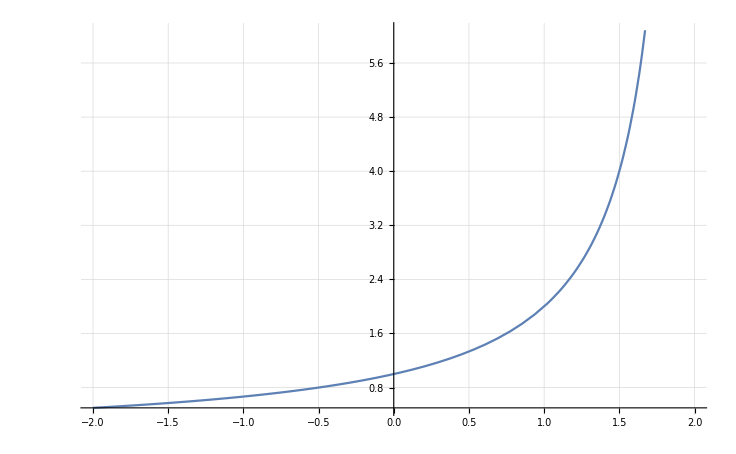

```mathematica
Plot[-2/(-2+x),{x,-2,2},GridLines->Automatic]
```